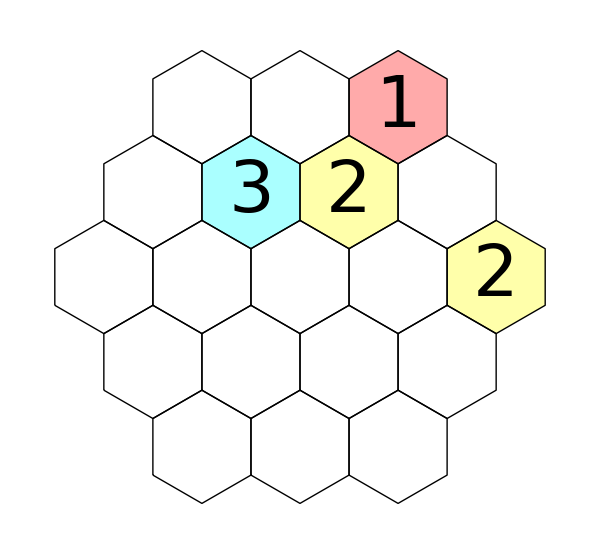

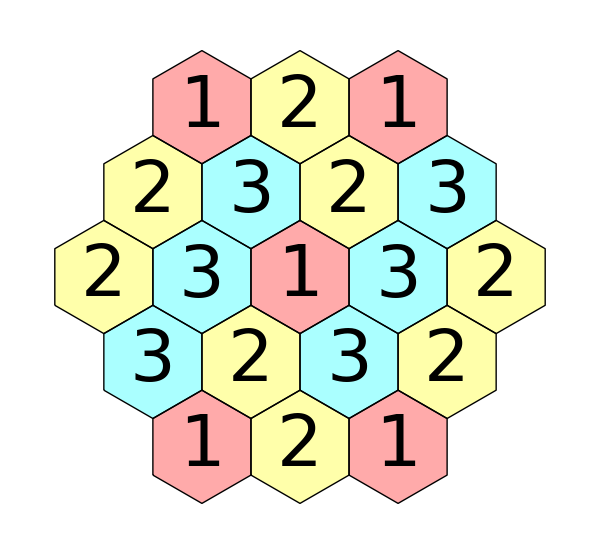

```mathematica
neigh={{1,0},{-1,0},{0,1},{0,-1}};
```

```mathematica
okayQ[A_,loc_]:=Module[{},
a=Extract[A,loc];
If[a==0,Return[True]];
block={loc};
While[neighbors=Complement[Select[Flatten[Outer[Plus,block,neigh,1],1],1≤#[[1]]≤n&&1≤#[[2]]≤n&&Extract[A,#]==a&],block];Length[neighbors]>0,block=block~Join~neighbors];
c=Extract[A,Complement[Select[Flatten[Outer[Plus,block,neigh,1],1],1≤#[[1]]≤n&&1≤#[[2]]≤n&],block]];
If[Length[block]>a,Return[False]];
(Length[block]==a)||MemberQ[c,0]]
```

```mathematica
okayQ[A_]:=Apply[And,Map[okayQ[A,#]&,Flatten[Table[{ii,jj},{ii,1,n},{jj,1,n}],1]]]
```

```mathematica
n=6;
stack={Table[0,{n},{n}]};
solns={};
While[Length[stack]>0,
cur=First[stack];
stack=Rest[stack];
pos=Position[cur,0];
If[pos=={},AppendTo[solns,cur],
pos=pos[[1]];
new=Select[Table[ReplacePart[cur,pos->kk],{kk,1,3}],okayQ];
stack=new~Join~stack;
]]
```

```mathematica
pic[A_]:=Graphics[{
MapIndexed[{Which[#1==1,Hue[0,1/3],
#1==2,Hue[1/6,1/3],
#1==3,Hue[1/2,1/3],
#1==4,Hue[3/4,1/5],
True,White],Rectangle[{#2[[1]],-#2[[2]]},{#2[[1]]-1,1-#2[[2]]}],Black,If[#1>0,Text[Style[#1,FontSize->16],{#2[[1]]-1/2,.45-#2[[2]]}],{}]}&,A,{2}],Style[{Table[Line[{{0,-i},{n,-i}}],{i,0,n}],Table[Line[{{i,0},{i,-n}}],{i,0,n}]},Antialiasing->False]
},ImageSize->20n+1,PlotRange->{{-.05,n+.05},{-n-.05,.05}}]
```

```mathematica
make[L_]:=Module[{},
A=Table[0,{n},{n}];
For[ii=1,ii≤Length[L],ii++,
A=ReplacePart[A,Drop[L[[ii]],-1]->Last[L[[ii]]]]];A]
```

```mathematica
restrict[L_]:=Module[{s=solns},
For[jj=1,jj≤Length[L],jj++,
s=Select[s,Extract[#,Drop[L[[jj]],-1]]==Last[L[[jj]]]&]];s]
```

```mathematica
Length[solns] (* 3x3 *)
```

38

```mathematica
Length[solns] (* 4x4 *)
```

152

```mathematica
Length[solns](* 5x5 *)
```

4460

```mathematica
Length[solns](* 6x6 *)
```

118164

```mathematica
r:={RandomInteger[{1,n}],RandomInteger[{1,n}],RandomInteger[{1,3}]}
```

```mathematica
n=6;
For[m=1,m>0,m++,
q={r,r,r,r,r};
s=restrict[q];
If[Length[s]==1,Print[pic[make[q]]];Print[pic[s[[1]]]]]]
```

$Aborted

## 5x5

-Graphics-

-Graphics-

-Graphics-

«345 more identical outputs»

## 6x6

-Graphics-

-Graphics-

-Graphics-

«169 more identical outputs»

## hex

```mathematica
neigh={{1,0},{-1,0},{0,1},{0,-1},{1,1},{-1,-1}};
```

```mathematica
p[x_,y_]:={2Sqrt[3]/2 x-y Sqrt[3]/2,1.5y }
p[{x_,y_}]:=p[x,y]

board[nn_]:={Table[hex[i,j],{j,1,nn},{i,1,nn-1+j}],
	Table[hex[i,j],{j,nn+1,2nn-1},{i,j-nn+1,2nn-1}]}

hex[x_,y_]:={
Line[{p[x,y]+{-Sqrt[3]/2,-1/2},p[x,y]+{-Sqrt[3]/2,1/2},p[x,y]+{0,1},p[x,y]+{Sqrt[3]/2,1/2},p[x,y]+{Sqrt[3]/2,-1/2},p[x,y]+{0,-1},p[x,y]+{-Sqrt[3]/2,-1/2}}]}

fillhex[z_,{x_,y_}]:=If[z==4,{},{Which[z==1,Hue[0,1/3],
z==2,Hue[1/6,1/3],
z==3,Hue[1/2,1/3],
True,White],
	Polygon[{p[x,y]+{-Sqrt[3]/2,-1/2},p[x,y]+{-Sqrt[3]/2,1/2},p[x,y]+{0,1},p[x,y]+{Sqrt[3]/2,1/2},p[x,y]+{Sqrt[3]/2,-1/2},p[x,y]+{0,-1},p[x,y]+{-Sqrt[3]/2,-1/2}}],Black,Text[If[0<z<4,z," "],p[x,y]]}]
```

```mathematica
okayQ[A_,loc_]:=Module[{},
a=Extract[A,loc];
If[a==0,Return[True]];
block={loc};
While[neighbors=Complement[Select[Flatten[Outer[Plus,block,neigh,1],1],1≤#[[1]]≤2n-1&&1≤#[[2]]≤2n-1&&Extract[A,#]==a&],block];Length[neighbors]>0,block=block~Join~neighbors];
c=Extract[A,Complement[Select[Flatten[Outer[Plus,block,neigh,1],1],1≤#[[1]]≤2n-1&&1≤#[[2]]≤2n-1&],block]];
If[Length[block]>a,Return[False]];
(Length[block]==a)||MemberQ[c,0]]
```

```mathematica
okayQ[A_]:=Apply[And,Map[okayQ[A,#]&,Select[Flatten[Table[{ii,jj},{ii,1,2n-1},{jj,1,2n-1}],1],Abs[#[[1]]-#[[2]]]<n&]]]
```

```mathematica
pic[A_]:=Graphics[{
MapIndexed[fillhex,A,{2}],board[n]
},ImageSize->18(2n-1)+1]
```

```mathematica
make[L_]:=Module[{},
A=Table[If[Abs[i-j]≥n,4,0],{i,2n-1},{j,2n-1}];
For[ii=1,ii≤Length[L],ii++,
A=ReplacePart[A,Drop[L[[ii]],-1]->Last[L[[ii]]]]];A]
```

```mathematica
restrict[L_]:=Module[{s=solns},
For[jj=1,jj≤Length[L],jj++,
s=Select[s,Extract[#,Drop[L[[jj]],-1]]==Last[L[[jj]]]&]];s]
```

```mathematica
n=3;
stack={Table[If[Abs[i-j]≥n,4,0],{i,2n-1},{j,2n-1}]};solns={};
While[Length[stack]>0,
cur=First[stack];
stack=Rest[stack];
pos=Position[cur,0];
If[pos=={},AppendTo[solns,cur],
pos=pos[[1]];
new=Select[Table[ReplacePart[cur,pos->kk],{kk,1,3}],okayQ];
stack=new~Join~stack;
]]
```

```mathematica
Length[solns] (* 2x2x2 *)
```

27

```mathematica
Length[solns] (* 3x3x3 *)
```

572

```mathematica
Length[solns] (* 4x4x4 *)
```

5563

```mathematica
r:=Module[{},
temp={RandomInteger[{1,2n-1}],RandomInteger[{1,2n-1}],RandomInteger[{1,3}]};
While[Abs[temp[[1]]-temp[[2]]]≥n,temp={RandomInteger[{1,2n-1}],RandomInteger[{1,2n-1}],RandomInteger[{1,3}]}];temp]
```

```mathematica
n=3;
For[m=1,m<1000,m++,
q={r,r,r,r,r};
s=restrict[q];
If[Length[s]==1,Print[pic[make[q]]];Print[pic[s[[1]]]]]]
```

### 3x3x3 - 5 clues

-Graphics-

-Graphics-

-Graphics-

«129 more identical outputs»

### 3x3x3 - 4 clues

-Graphics-

-Graphics-

-Graphics-

«89 more identical outputs»